```mathematica
ClearAll[x]
```

```mathematica
eqn1=x''[t] == β x'[t] h'[t]
eqn2=h''[t] == (1-β/2) h'[t]^2 - β x'[t]^2/2
```

x''[t]==β h'[t] x'[t]

h''[t]==(1-β/2) h'[t]^2-1/2 β x'[t]^2

```mathematica
bc={x[0]== 0, x[tf]== xf, h[0]==0, h[tf]==0}
```

{x[0]==0,x[tf]==xf,h[0]==0,h[tf]==0}

```mathematica
rules={β-> 3.95, xf->1, tf->1.}
```

{β→3.95,xf→1,tf→1.}

```mathematica
sol=NDSolve[({eqn1, eqn2,bc}//Flatten)/.rules,{x[t],h[t]},{t,0,tf}/.rules,Method->{"Shooting", "StartingInitialConditions"-> ({x[tf/2]==xf/2, h[tf/2] == 0.5}/.rules)}]
```

{{x[t]→InterpolatingFunction[{{0., 1.}}, <>][t],h[t]→InterpolatingFunction[{{0., 1.}}, <>][t]}}

```mathematica
x[t]/.sol/.t-> 0
```

{1.93444×10^-8}

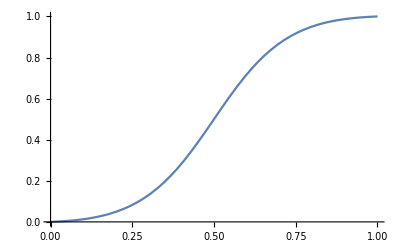

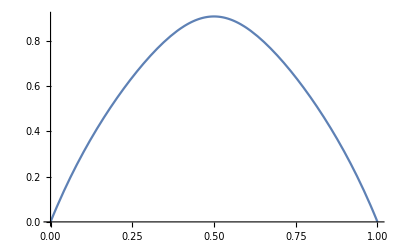

```mathematica
Plot[x[t]/.sol,{t,0,tf}/.rules,PlotRange->Full]
Plot[h[t]/.sol,{t,0,tf}/.rules,AxesOrigin->{0,0},PlotRange->Full]
ParametricPlot[{x[t],h[t]}/.sol,{t,0,tf/.rules}]
```

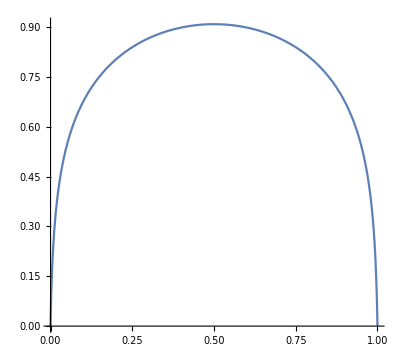
```mathematica
g6=-Graphics-
```

-Graphics-

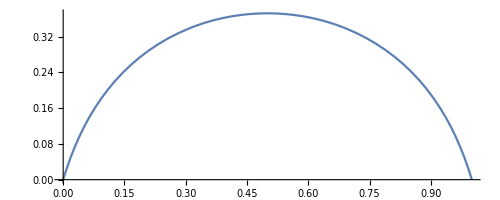
```mathematica
g5=-Graphics-
```

-Graphics-

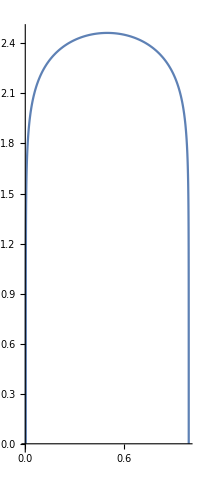
```mathematica
g4=-Graphics-
```

-Graphics-

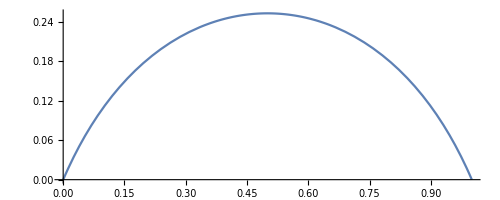
```mathematica
g3=-Graphics-
```

-Graphics-

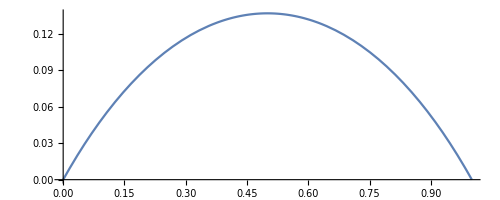
```mathematica
g2=-Graphics-
```

-Graphics-

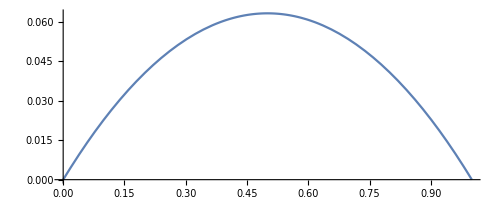
```mathematica
g1=-Graphics-
```

-Graphics-

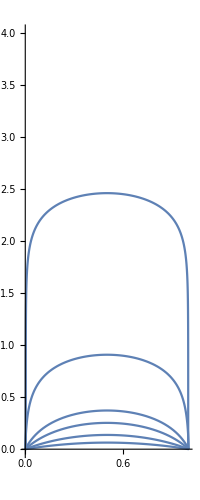

```mathematica
Show[{g1,g2,g3,g4,g5,g6},PlotRange-> {{0,1},{0,4}}]
```

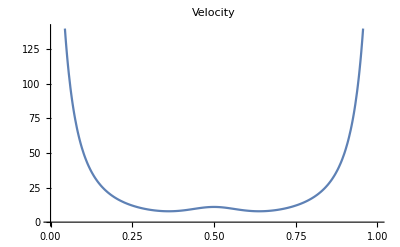

```mathematica
Plot[((D[x[t]/.sol[[1]],t]/.t-> t2)^2+(D[h[t]/.sol[[1]],t]/.t-> t2)^2),{t2,0,tf/.rules},PlotLabel->"Velocity"]
```

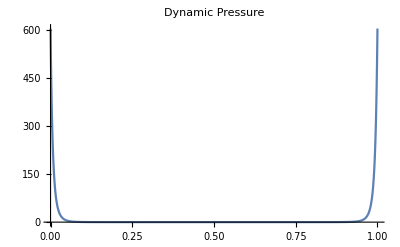

```mathematica
Plot[(Exp[-β h[t]/.sol/.rules]/.t-> t2)((D[x[t]/.sol[[1]],t]/.t-> t2)^2+(D[h[t]/.sol[[1]],t]/.t-> t2)^2),{t2,0,tf/.rules},PlotRange->Full,PlotLabel->"Dynamic Pressure"]
```

```mathematica
vx=(D[x[t]/.sol[[1]],t]/.t-> t2)
vh=(D[h[t]/.sol[[1]],t]/.t-> t2)
```

InterpolatingFunction[{{0., 1.}}, <>][t2]

InterpolatingFunction[{{0., 1.}}, <>][t2]

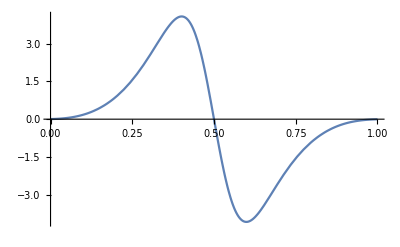

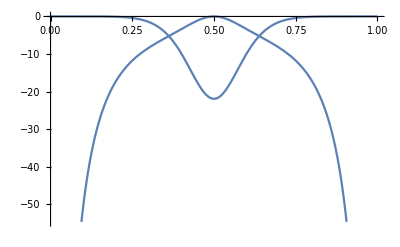

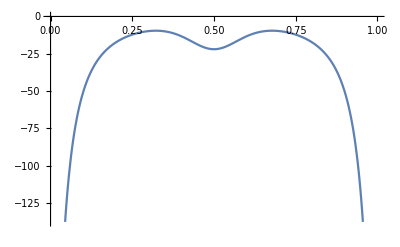

```mathematica
Plot[vx vh,{t2,0,tf/.rules}]
Plot[{(1-β/2) vh^2 ,-β vx^2/2}/.rules,{t2,0,tf/.rules}]
Plot[{(1-β/2) vh^2 -β vx^2/2}/.rules,{t2,0,tf/.rules}]
```